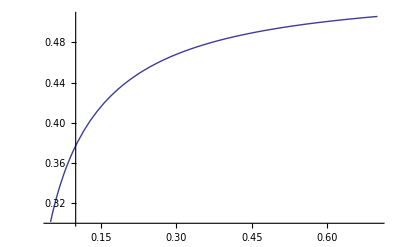

```mathematica
λ=1.175;
func[θB_,x0_,am_]:=NIntegrate[ArcTan[x0/Sqrt[w^2+am^2]]*4/Sqrt[w^2+am^2],{w,0,θB}]
norm[am_]:=1/(2π)(NIntegrate[a/(a^2+am^2),{a,0,π/2}])^-1
th[qz_]:=λ qz/(4π)
Plot[norm[0.05*π/180]*func[th[qz],1.4*π/180,0.05*π/180],{qz,0.05,0.7}]
```

```mathematica
Export["~/mosaic_correction.dat",Table[{qz,norm[0.05*π/180]*func[th[qz],1.4*π/180,0.05*π/180]},{qz,0.05,0.7,0.001}]]
```

~/mosaic_correction.dat

```mathematica
am=0.05*π/180;
tb=90*π/180;
x0=1.4*π/180;
norm[am]*func[tb,x0,am]
```

0.535754

```mathematica
am=0.1*π/180;
tb=4*0.58*π/180;
x0=1.4*π/180;
norm[am]*func[tb,x0,am]/(norm[am]*func[tb,45*π/180,am])
```

0.778811